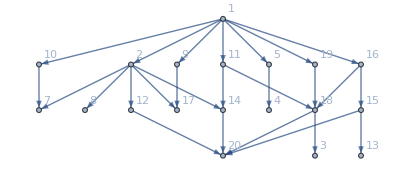

```mathematica
SeedRandom[123123];
g1=Graph[WeaklyConnectedGraphComponents[ResourceFunction["ToDirectedAcyclicGraph"][RandomGraph[{20,40}],1]][[1]],VertexCoordinates->Automatic,VertexLabels->"Name",GraphLayout->Automatic]
```

```mathematica
ResourceFunction["BacktrackSearch"][{{1},VertexList[g1],VertexList[g1],VertexList[g1]},MemberQ[EdgeList[g1],DirectedEdge@@#[[-2;;-1]]]&,True&,All]
```

{{1,2,12,20},{1,2,14,20},{1,11,14,20},{1,11,18,20},{1,11,18,3},{1,16,18,20},{1,16,18,3},{1,16,15,20},{1,16,15,13},{1,19,18,20},{1,19,18,3}}